# Homework 12 Notebook

## Steve Turley: Physics 222, 10/6/2011

This notebook has some Mathematica examples of wave packets I would like you to experiment with for part of your homework.  When you've done the assigned work, save the notebook as a PDF file  (File/Save As/PDF Document) and submit the document online.

Be sure to open any hidden sections before saving the file as a PDF document.  Any sections which are not visible in the notebook at the time you save it will not be visible in the PDF document either.

## Minimum Uncertainty Wave Packets

Gaussian wave packets are the best example I know of smoothly varying wave packets which transform easily.  They are called minimum uncertainty wave packets becuase they minimize the product of ΔxΔk.

### Stationary Wave Packet

This is the gaussian envelope of a wave packet.  The argument x is the position at which the wave packet is evaluated.  The argument sigma controls the width of the wave packet.

```mathematica
psix[x_,σ_]:=1/(Pi^(1/4)Sqrt[σ])*Exp[-x^2/(2*σ^2)]

psix[x,σ]//TraditionalForm
```

(ⅇ^(-x^2/(2 σ^2)))/(π^(1/4) √σ)

The packet is normalized so that the area of its square is equal to one.  That means that the square of the wave packet can be interpreted as a probability density.

```mathematica
Integrate[psix[x,σ]^2,{x,-Infinity,Infinity},Assumptions->σ>0]
```

1

By multiplying the packet by a complex plane wave, we know have a packet with an approximate value of k.

```mathematica
psix[x_,σ_,k_]:=psix[x,σ]*Exp[I*k*x]
```

Since the magnitude of Exp[I*k*x] is equal to one, this packet is still normalized.

```mathematica
Integrate[Abs[psix[x,σ,k]]^2,{x,-Infinity,Infinity},Assumptions->σ>0 && Element[k,Reals]]
```

1

Here is a plot of the real and imaginary parts of the wave packet.

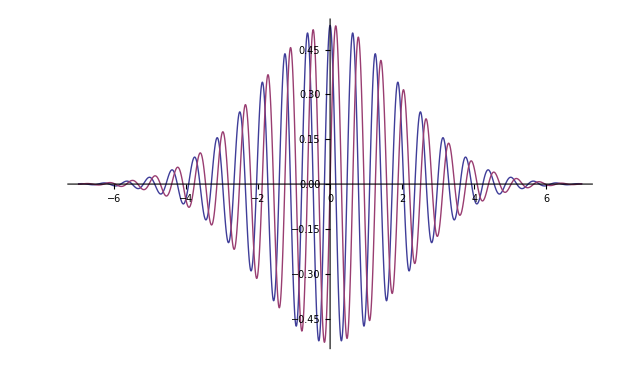

```mathematica
Plot[{Re[psix[x,2,10]],Im[psix[x,2,10]]},{x,-7,7}, PlotRange->All]
```

For clarity, let's plot the real and imaginary parts separately.  Here is the real part.

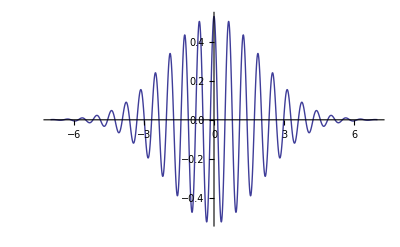

```mathematica
Plot[Re[psix[x,2,10]],{x,-7,7}, PlotRange->All]
```

Here is the imaginary part.

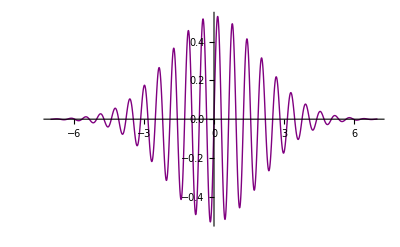

```mathematica
Plot[Im[psix[x,2,10]],{x,-7,7}, PlotRange->All,PlotStyle->Purple]
```

Now, let's plot the probability density, which is the square of the wave function.

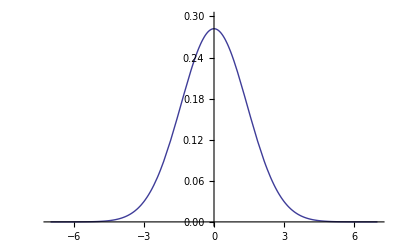

```mathematica
Plot[Abs[psix[x,2,10]]^2,{x,-7,7}, PlotRange->{0,.3}]
```

ASSIGNMENT: Estimate the width of the probability density above.  A reasonable estimate of the width would be the half width at half maximum.  This is the distance between center of the curve and one of the sides of the curve when the curve has a value of half its maximum height.  Write your answer below:

```mathematica
Maximize[Abs[psix[x,2,10]],x]//N
```

{0.531126,{x→-7.45058×10^-9}}

ANSWER:  Max is about .28, so half maximum is about .14. The 1/2 width there is about 2.

ASSIGNMENT:  Compare the half width at half maximum to the parameter sigma.  (What is the ratio of the two?)

ANSWER:  σ/HMHW = 2/2 = 1

ASSIGNMENT:  Now plot a curve with a sigma of 1 instead of two.  What is the half width at half maximum in this case?  How does it compare to the new value of sigma?

PLOT:

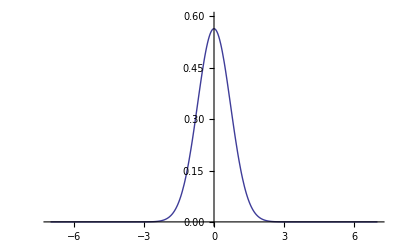

```mathematica
Plot[Abs[psix[x,1,10]]^2,{x,-7,7},PlotRange->{0,.6}]
```

WIDTH: the max is about .56, so 1/2 of that is about .28. The 1/2 width there is about 1 so the ratio is 1/1 = 1. (same ratio as above).

### Momentum Distribution

Mathematica has a very useful set of functions for doing Fourier transforms and inverse Fourier transforms.  The inverse Fourier transform of a wave function give the amplitude of the various plane wave components.

```mathematica
kspace=InverseFourierTransform[Evaluate[psix[x,σ,k]],x,kp, Assumptions->Element[σ,Reals]]
```

(√(σ^2) ⅇ^(-1/2 σ^2 (kp-k)^2))/(π^(1/4) √σ)

Define k-space wave function

```mathematica
psik[kp_,σ_,k_]:=Evaluate[kspace]
```

This wave packet has the same normalization as the wave packet for the position of the particle.

```mathematica
Integrate[psik[kp,σ,k]^2,{kp,-Infinity,Infinity}, Assumptions->σ>0]
```

1

Plot k-space wave function

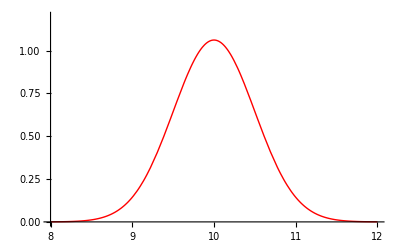

```mathematica
kspacewaveplot=Plot[psik[kp,2,10],{kp,8,12},PlotRange->{0,1.2},PlotStyle-> Red]
```

Note that this function is centered about the central wave number k=10 from the original wave packet, but that it's spread out a bit.  In other words, a range of k values was necessary in order to get a well defined wave packet.

Let's plot the probability density of this wave packet in order to find the width in k of this distribution.  This is the probability density of the particle having a particular value of kp between kp and kp+dkp.

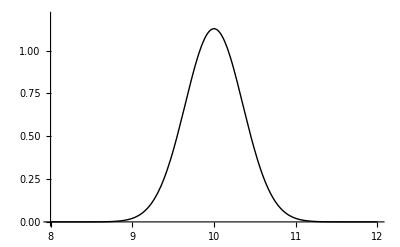

```mathematica
kspacedensityplot = Plot[psik[kp,2,10]^2,{kp,8,12},PlotRange->{0,1.2},PlotStyle->Black]
```

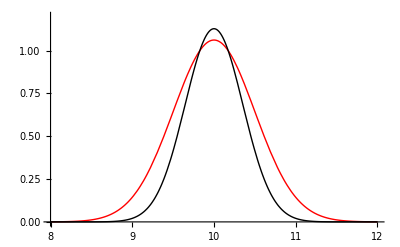

0.531126

0.56419

```mathematica
Show[kspacewaveplot,kspacedensityplot]
psik[10,2,10]/2//N
psik[10,2,10]^2/2//N
```

ASSIGNMENT:  What is the width of this wave packet?  How does it compare to the width of the position probability density?

ANSWER: Width (HWHM): The width of the wave packet (both sides) is about .6 and the width of the density function is about .4.

ASSIGNMENT:  Plot the k probability density of a wavepacket with sigma=1 instead of sigma=2.  What is its width?  Discuss how that compares with the width of the other k probability density with sigma=2 and with the width of the position wave packet for sigma=1 you found earlier.

PLOT:

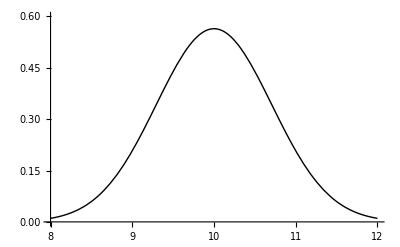

0.282095

```mathematica
Plot[psik[kp,1,10]^2,{kp,8,12},PlotRange->{0,.6},PlotStyle->Black]
psik[10,1,10]^2/2//N
```

ANSWER: This time the density function is about twice as wide with σ=1 instead of σ=2. That is the opposite effect we saw in the first example.

### Travelling Wave Packets

A wave packet which just sits in one spot isn't very interesting.  (It's also not physically possible.)  In fact, each of the sinusoidal waves making up the wave packet will be moving.  The movement can be accomplished by replacing the stationary waves with wave functions Exp[I*k*x] with travelling waves Exp[I*(k*x-omega*t)].  These will be waves moving with a speed of omega/k.

If I take the inverse Fourier transform of the waves replacing x with x-vt=x-omega/k*t, I will get a moving wave packet.

```mathematica
xtft=FourierTransform[Evaluate[psik[kp,σ,k]],kp,x-ω/k*t];
```

```mathematica
psix[x_,σ_,k_,ω_,t_]:=Evaluate[xtft]
```

With a speed of 0 (corresdponding to omega=0), it should have the same functional form as my original wave packet.

```mathematica
psix[x,σ,k,0,t]//OutputForm
```

2  2         2
 (x (-(k x) + (2 I) k  σ ))/(2 k σ )
E
------------------------------------
             1/4
           Pi    Sqrt[σ]

```mathematica
Simplify[psix[x,σ,k,0,t], Assumptions->σ>0]//StandardForm
```

(ⅇ^(ⅈ k x-x^2/(2 σ^2)))/(π^(1/4) √σ)

Let's look at this in an animation and see what it looks like with a sigma=2, k=10, and an omega=1.  This means it's speed is omega/k=1/10.  I've displayed t as the plot label so you can check the speed.

```mathematica
Animate[Plot[Abs[psix[x,2,10,1,t]]^2,{x,-7,40}, PlotRange->{{0,40},{0,0.3}}, PlotLabel->t],{t,0,400}]
```

ASSIGNMENT:  Create an animated plot of a moving wave packet with a width sigma=1, a value of k of 5, and a speed of 0.5.  You might need to play with the ranges for the plot and the time to get it to look reasonably.

PLOT:

```mathematica
(*if speed = 0.5 and k =5, ω = .5*5 = 1.5 *)
Animate[Plot[Abs[psix[x,1,5,2.5,t]]^2,{x,-7,40},PlotRange->{{0,40},{0,0.6}},PlotLabel->t],{t,0,100}]
```

## Square Wave Packet

Another way to construct a wave packet is to put a square envelope on the underlaying sinusoidal wave.  In other words, the wave will have a constant amplitude inside a certain limit and be zero outside that limit.  Here's a function that computes such a wave packet.

### Spatial wave packet

```mathematica
sqx[x_,w_,k_]:= UnitBox[x/w]/Sqrt[w]*Exp[I*k*x]
```

Here is a plot of the real and imaginary parts of the wave function.

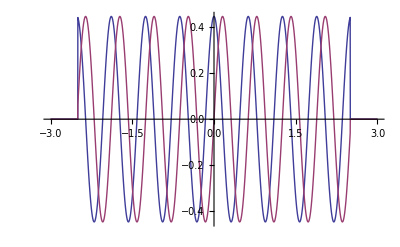

```mathematica
Plot[{Re[sqx[x,5,10]],Im[sqx[x,5,10]]},{x,-3,3}]
```

This wave function is correctly normalized to 1.

```mathematica
Integrate[(Abs[sqx[x,w,k]])^2,{x,-Infinity,Infinity}, Assumptions->Element[k, Reals] && w>0]
```

1

The probability density is pretty simple.

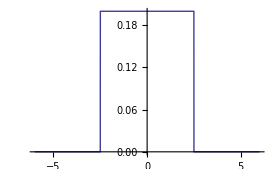
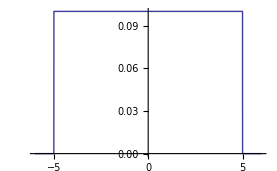

```mathematica
Row[{Plot[(Abs[sqx[x,5,10]])^2,{x,-6,6},PlotRange->All],Plot[(Abs[sqx[x,10,10]])^2,{x,-6,6},PlotRange->All]}]
```

ASSIGNMENT:  What is the half width at half max of this distribution?

ANSWER: Same as the half width at max! it is 2.5.

ASSIGNMENT:  What would the half width be with w=10?  (No need to plot this or make special functions.)

ANSWER:  I’m going to guess that it is 5. Yep, that’s right

### Momentum wave packet

We can see what values of k need to integrated together to construct this wave packet by taking the inverse Fourier transform as before.

```mathematica
ksq=InverseFourierTransform[Evaluate[sqx[x,w,k]],x,kp, Assumptions->Element[w,Reals]]
```

(√(2/π) (w--w) sin(1/2 w (k-kp)))/(√w (k-kp))

```mathematica
sqk[kp_,w_,k_]:=Evaluate[ksq]
```

If we plot the square of this (note that it's real), we will have the probability density.

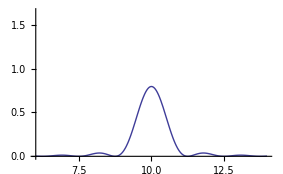
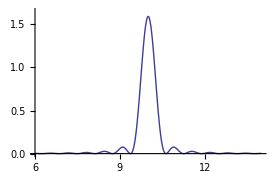
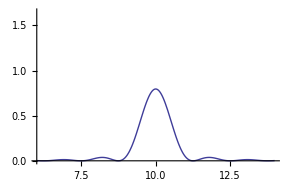
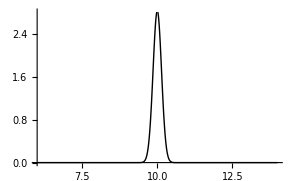
Grid[{-Graphics--Graphics-,-Graphics--Graphics-}]

```mathematica
Grid[{Row[{Plot[sqk[kp,5,10]^2,{kp,6,14},PlotRange->{0,1.65}],Plot[sqk[kp,10,10]^2,{kp,6,14},PlotRange->{0,1.65}]}],Row[{Plot[sqk[kp,5,10]^2,{kp,6,14},PlotRange->{0,1.65}],Plot[psik[kp,5,10]^2,{kp,6,14},PlotRange->{0,2.8},PlotStyle->Black]}]}]
```

ASSIGNMENT: Comment  on the differences between the distribution of k for a square wave packet and a minimum uncertainty (gaussian) wave packet.  (How do widths and shapes compare for comparable widths in position?)

ANSWER : See plot above,  2nd row. The things I see are that the Gaussian wave packet actually has a PDF that is a bit smoother, it is much taller, much narrower, and it doesn’t bounce around 0 when it heads that direction.

ASSIGNMENT:  Look at the wave number distribution for a wave packet with w=10 instead of w=5.  How does the width compare between the two distributions?

PLOT: See above,  first row.

```mathematica
(* See above *)
```

COMPARISON: The width is 1/2 as much if ω =10 as it is when ω = 5.